0.724406

```mathematica
2^3 3^2 5
```

360

```mathematica
Clear[step,r]
n1=720;
n2=2n1;
r1=3;
r2=4;
step[0]=Random[]
step[i_]:=step[i]=(r1+(r2-r1)i/(n1 n2))step[i-1](1-step[i-1])
off=.5;
(*step/@Range[n^2];*)
f=Fourier[step/@Range[n1#,n1#+n1-1]-off]&/@Range[0,n2-1];
ArrayPlot[Transpose@(Abs[f])^(1/4),ImageSize->n2]
```

0.405303

-Graphics-

```mathematica
ArrayPlot[Transpose@Abs[f],PixelConstrained->{1,1},ColorFunction->(GrayLevel[#^(1/2)]&),ColorFunctionScaling->True]
```

-Graphics-

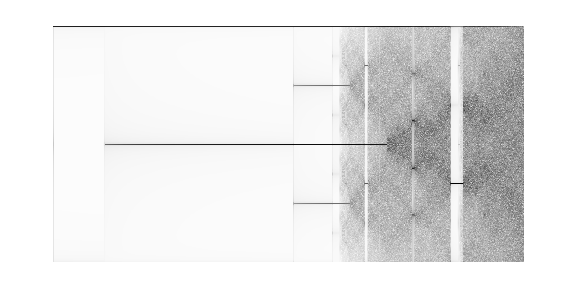

```mathematica
ArrayPlot[Transpose@(Abs[f])^(1/3),ImageSize->n2]
```

```mathematica
MatrixPlot[Transpose@Arg[f],ImageSize->n1,ColorFunction->Hue]
```

-Graphics-

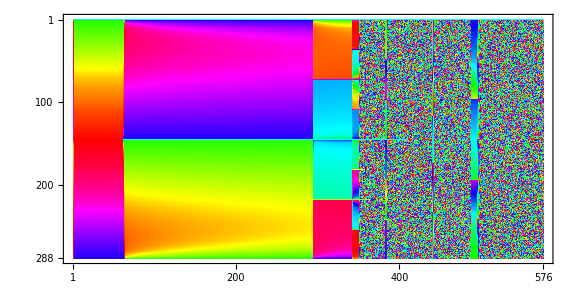

```mathematica
MatrixPlot[Transpose@Arg[f],ImageSize->n2,ColorFunction->Hue]
```

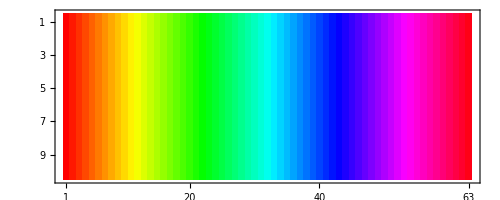

```mathematica
MatrixPlot[Range[-Pi,Pi,.1]&/@Range[10],ColorFunction->Hue]
```

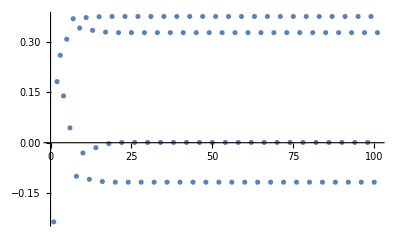

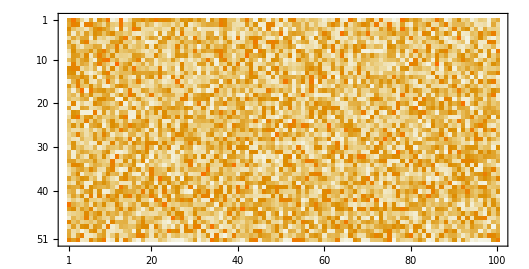

```mathematica
ListPlot[step/@Range[0,100]-.5]
```

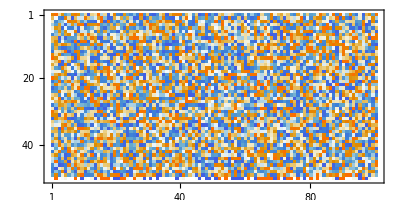

```mathematica
MatrixPlot[Transpose@Arg[%19[[All,2;;51]]]]
```

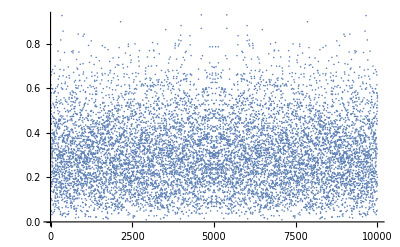

```mathematica
ListPlot[Abs[%13]]
```

```mathematica
ArrayPlot[(Mod[#,2]&/@Range[200])&/@Range[200],PixelConstrained->True]
```

-Graphics-